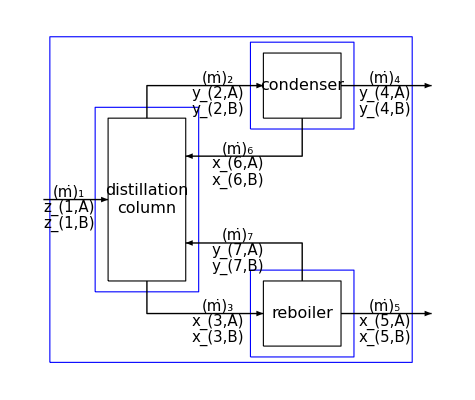

```mathematica
Module[{species,convert,unit,border,flowText,compText,equipment,streams,variables},
species=2;
convert={1->"A",2->"B",3->"C",4->"D"};

unit[pos_,side_]:=Rectangle[{pos[[1]]-1.5,pos[[2]]-side*1.5},{pos[[1]]+1.5,pos[[2]]+side*1.5}];
border[pos_,side_]:=Rectangle[{pos[[1]]-2,pos[[2]]-(side*1.5+0.5)},{pos[[1]]+2,pos[[2]]+(side*1.5+0.5)}];

(**)flowText[number_,pos_]:=Text[Style[Subscript[OverDot@Style["m",Italic],number],15],pos,{0,-1.5}];
(**)compText[comp_,number_,pos_]:=
Text[Style[Subscript[Style[comp,Italic],Row@{number,",",ReplaceAll[#,convert]}],15],{pos[[1]],pos[[2]]-(#-1)*0.75},{0,1.15}]&/@Range@species;

equipment={
{"distillation column",unit[{0,0},2.5],border[{0,0},2.5],Text[Style[Column[{"distillation","column"},Center],16],{0,0}]},
{"condenser",unit[{6,5.25},1],border[{6,5.25},1],Text[Style["condenser",16],{6,5.25}]},
{"reboiler",unit[{6,-5.25},1],border[{6,-5.25},1],Text[Style["reboiler",16],{6,-5.25}]}};

streams={Arrow[{{-4,0},{-1.5,0}}],Arrow[{{0,3.75},{0,5.25},{4.5,5.25}}],Arrow[{{0,-3.75},{0,-5.25},{4.5,-5.25}}],Arrow[{{7.5,5.25},{11,5.25}}],Arrow[{{7.5,-5.25},{11,-5.25}}],Arrow[{{6,3.75},{6,2},{1.5,2}}],Arrow[{{6,-3.75},{6,-2},{1.5,-2}}]};

(**)variables={
{"feed",flowText[1,{-3,0}],compText["z",1,{-3,0}]},
{"vapor",flowText[2,{2.75,5.25}],compText["y",2,{2.75,5.25}]},
{"liquid",flowText[3,{2.75,-5.25}],compText["x",3,{2.75,-5.25}]},
{"overhead",flowText[4,{9.2,5.25}],compText["y",4,{9.2,5.25}]},
{"bottoms",flowText[5,{9.2,-5.25}],compText["x",5,{9.2,-5.25}]},
{"reflux",flowText[6,{3.5,2}],compText["x",6,{3.5,2}]},
{"reboil",flowText[7,{3.5,-2}],compText["y",7,{3.5,-2}]}};

Graphics[{
{EdgeForm[Thick],FaceForm[None],equipment[[All,2]]},
{EdgeForm[{Thick,Dashed,Blue}],FaceForm[None],equipment[[All,3]],Rectangle[{-3.75,-7.5},{10.25,7.5}]},
equipment[[All,4]],{Thick,streams},Drop[variables,None,1]
},ImageSize->{475,400},AspectRatio->Full,PlotRange->{-7.55,7.51}]
]
```

```mathematica
(*(**)variables={
{"feed",flowText[1,{-3,0}],compText["z",{-3,0}]},
{"vapor",flowText[2,{2.75,5.25}],compText["y",{2.75,5.25}]},
{"liquid",flowText[3,{2.75,-5.25}],compText["x",{2.75,-5.25}]},
{"overhead",flowText[4,{9.2,5.25}],compText["y",{9.2,5.25}]},
{"bottoms",flowText[5,{9.2,-5.25}],compText["x",{9.2,-5.25}]},
{"reflux",flowText[6,{3.5,2}],compText["x",{3.5,2}]},
{"reboil",flowText[7,{3.5,-2}],compText["y",{3.5,-2}]}};*)
```

```mathematica
Module[{species,compText},
species=2;
(*compText[comp_,pos_]:=Text[Style[Subscript[Style[comp,Italic],#],15],{pos[[1]],pos[[2]]-(#-1)*0.75},{0,1.15}]&/@Range@species;*)
(*compText[comp_,number_,pos_]:=Text[Style[Subscript[Style[comp,Italic],Row@{number,",",#}],15],pos,{0,1.15*#}]&/@{1,2};*)
(*compText[comp_,number_,pos_]:=Text[Style[Subscript[Style[comp,Italic],Row@{number,",",#2}],15],pos,{0,1.15*Flatten@#1}]&@@@{{{1,2},{"A","B"}}};*)
compText[comp_,number_,pos_]:=Table[Text[Style[Subscript[Style[comp,Italic],Row@{number,",",#2[[i]]}],15],pos,{0,1.15*#1[[i]]}]&@@@{{{1,2},{"A","B"}}},{i,{1,2}}];

Graphics@compText["z",3,{0,0}]
]
```

-Graphics-

```mathematica
{#1,#2}&@@@{{1,2},{"A","B"}}
```

{{1,2},{A,B}}

```mathematica
#1&@@@{1,2,"A","B"}
```

{1,2,A,B}

```mathematica
Module[{L0,L1,L2,L3},
L0={1,2,A,B};
L1=Partition[L0,2];

Graphics[
Text[#2,{0,#1}]&@@@{{{1,2},{"A","B"}}}
]
]
```

-Graphics-

```mathematica
(*Column[{
L1,
Flatten[#1&@@@{L1}],
#2&@@@{L1}
}]*)
```

```mathematica
Module[{l2n},
l2n={"A"->1,"B"->2,"C"->3};
Replace[{"A","B"},l2n]
]
```

{A,B}